## Reference for testing interpolation functionality

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SeedRandom[1420000241];
```

```mathematica
Subscript[f, grid]=(Append[#,First[#]+{1,{0,0,0,0}}])&[Table[{x,{Exp[Sin[2π x]],ArcTan[Cos[π x]^2],Sin[4π x]+RandomReal[{-0.02,0.02}],Sin[2π x]+Cos[16π x]/8}},{x,0,1-1/64,1/64}]];
Dimensions[%]
```

{65,2}

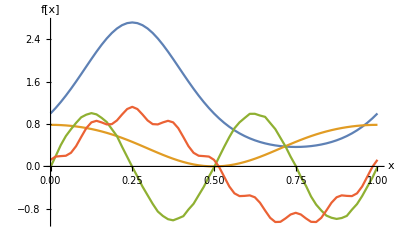

```mathematica
ListLinePlot[Table[{First[#],Last[#]⟦i⟧}&/@Subscript[f, grid],{i,4}],AxesLabel->{"x","f[x]"}]
```

```mathematica
(* save to disk *)
Export["interpolation_test_f_grid.dat",Flatten[Last/@Most[Subscript[f, grid]]],"Real64"];
```

```mathematica
(* perform interpolation *)
Subscript[f, ip]=Interpolation[Subscript[f, grid],PeriodicInterpolation->True]
```

InterpolatingFunction[{{…, 0., 1., …}}, <>]

```mathematica
(* example *)
Subscript[f, ip][0.3]
```

{2.58843,0.332652,-0.57629,0.850516}

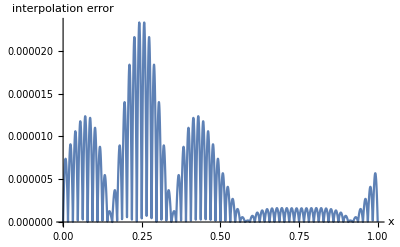

```mathematica
(* interpolation error of first component *)
Plot[Abs[Exp[Sin[2π x]]-First[Subscript[f, ip][x]]],{x,0,1},PlotRange->All,AxesLabel->{"x","interpolation error"}]
```

```mathematica
Prime[33]
```

137

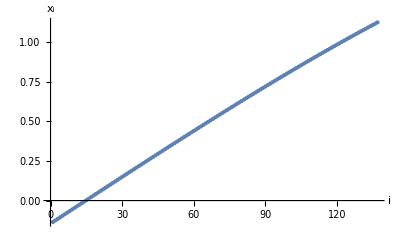

```mathematica
(* evaluation points *)
Subscript[x, eval]=Table[N[i/126-1/2+AiryAi[-i/137]],{i,137}];
ListPlot[%,AxesLabel->{"i","x_i"},PlotStyle->{PointSize[Small]}]
```

```mathematica
(* save evaluation points to disk *)
Export["interpolation_test_x_eval.dat",Subscript[x, eval],"Real64"];
```

```mathematica
(* save interpolated function values as reference to disk *)
Export["interpolation_test_f_eref.dat",Flatten[Subscript[f, ip]/@Subscript[x, eval]],"Real64"];
```